```mathematica
<<"C:\\Users\\aliha\\Desktop\\scripts-codes\\github codes\\UNET-Segmentation-Wolfram\\UNET.m";
dirimg="C:\\Users\\aliha\\Downloads\\fabrice-ali\\deeplearning\\data\\train\\train_images_8bit"; 
dirmasks="C:\\Users\\aliha\\Downloads\\fabrice-ali\\deeplearning\\data\\train\\train_masks";
```

```mathematica
{X,Y}=dataPrep[dirimg,dirmasks];
```

```mathematica
nNet=UNET
```

NetGraph[<>]

```mathematica
nNetInfo=trainNet[nNet,X[[;;300]],Y[[;;300]]]
```

NetTrainResultsObject[<>]

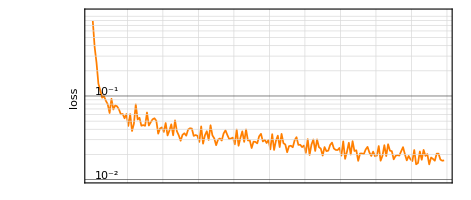

```mathematica
nNetInfo["LossEvolutionPlot"]
```

```mathematica
nNetTrained=nNetInfo["TrainedNet"]
```

NetGraph[<>]

```mathematica
generateImage[]:=With[{imgs=Thread[{X[[301;;]],Y[[301;;]]}]},
MapAt[NetDecoder[{"Image"}],RandomChoice@imgs,2]
]
```

```mathematica
{img,ground}=generateImage[]
```

{-Graphics-,-Graphics-}

```mathematica
{img,#,ground,HighlightImage[img,MorphologicalPerimeter@Binarize@#]}&[NetDecoder[{"Image"}]@nNetTrained[img,TargetDevice-> "GPU"]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
accuracy=measureModelAccuracy[nNetTrained,X[[301;;]],Y[[301;;]] ];
```

```mathematica
Style["Mean accuracy: "<>ToString@#,{RandomColor[],FontSize->29}]&@First@accuracy
```

Mean accuracy: 0.986467

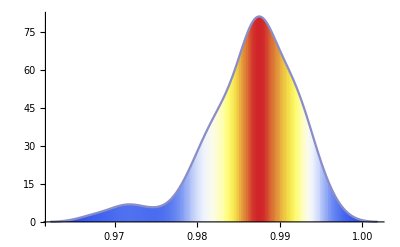

```mathematica
SmoothHistogram[(Last@accuracy)[[1,All,2]],ColorFunction->(ColorData["TemperatureMap"]),Filling->Axis]
```

```mathematica
saveNeuralNet[nNetTrained]
```

C:\Users\aliha\Desktop\UNET\unet.wlnet

## Import Net and apply

```mathematica
nNetTrained=Import["C:\\Users\\aliha\\Desktop\\scripts-codes\\github codes\\UNET-Segmentation-Wolfram\\unet.wlnet"]
```

NetGraph[<>]

```mathematica
testdata = X[[301;;]];
```

```mathematica
res=NetDecoder[{"Image"}]@nNetTrained[testdata,TargetDevice-> "GPU"];
```

```mathematica
If[ValueQ[testdata]&&ValueQ[res],
Manipulate[HighlightImage[testdata[[i]],res[[i]]],{i,1,Length@testdata,1}]
]
```

```mathematica
Rasterize@Grid[Partition[MapThread[Thumbnail[HighlightImage[#1,#2],100]&,{testdata,res}],10]]
```

-Graphics-